## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/slice/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.0798974 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Feb 29, 2020, time: 17:52:41

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/slice/slicer-02.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.0798974 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 1 read E fields from *.txt file

```mathematica
file="repaired-mesh.4112";
```

### point to file

```mathematica
dirMoM=dirData;
```

### read file to scan for data sets

```mathematica
strmList=Import[dirMoM<>file<>".txt","Data"]
title="Sciacca Airframe";
Λ=Dimensions[strmList]
```

{ ,---| Run Date: February  18, 2020;    Time: 16:03:53,14868,--------------------------------------------------------------------------------}
 |  |  |  |

{14871}

## 2 find table

### tag data sets: record line numbers

```mathematica
(* each data set represents a unique frequency *)
```

```mathematica
census={};
Table[
If[StringContainsQ[strmList[[k]],"Theta, Phi, Theta-Theta"],AppendTo[census,k]]
,{k,Length[strmList]}];
census
m=Length[census]
```

{492,1007,1522,2037,2552,3067,3582,4097,4612,5127,5642,6157,6672,7187,7702,8217,8732,9247,9762,10277,10792,11307,11822,12337,12852,13367,13882,14397}

28

#### empty containers for E field values

```mathematica
θθ={};
θϕ={};
ϕθ={};
ϕϕ={};
```

### harvest frequencies

```mathematica
frequencies={};
Table[
If[StringContainsQ[strmList[[k]],"Freq   ="],AppendTo[frequencies,StringSplit[strmList[[k]]]]]
,{k,Length[strmList]}];
frequencies
```

{{Freq,=,3.00E+00,MHz},{Freq,=,4.00E+00,MHz},{Freq,=,5.00E+00,MHz},{Freq,=,6.00E+00,MHz},{Freq,=,7.00E+00,MHz},{Freq,=,8.00E+00,MHz},{Freq,=,9.00E+00,MHz},{Freq,=,10.00E+00,MHz},{Freq,=,11.00E+00,MHz},{Freq,=,12.00E+00,MHz},{Freq,=,13.00E+00,MHz},{Freq,=,14.00E+00,MHz},{Freq,=,15.00E+00,MHz},{Freq,=,16.00E+00,MHz},{Freq,=,17.00E+00,MHz},{Freq,=,18.00E+00,MHz},{Freq,=,19.00E+00,MHz},{Freq,=,20.00E+00,MHz},{Freq,=,21.00E+00,MHz},{Freq,=,22.00E+00,MHz},{Freq,=,23.00E+00,MHz},{Freq,=,24.00E+00,MHz},{Freq,=,25.00E+00,MHz},{Freq,=,26.00E+00,MHz},{Freq,=,27.00E+00,MHz},{Freq,=,28.00E+00,MHz},{Freq,=,29.00E+00,MHz},{Freq,=,30.00E+00,MHz}}

### reader

```mathematica
nAngles=361;
```

```mathematica
Do[
myLine=census[[k]]+1;
fields=Table[
str=StringSplit[strmList[[myLine+j]]];
str=StringReplace[#,","->""]&/@str;
str=StringReplace[#,"("->""]&/@str;
str=StringReplace[#,")"->""]&/@str;
str=StringReplace[#,"{"->""]&/@str;
str=StringReplace[#,"}"->""]&/@str;
tbl=Read[StringToStream[#],Number]&/@Flatten[str]
,{j,nAngles}];
AppendTo[θθ,fields[[All,3]]+ⅈ fields[[All,4]]];
AppendTo[θϕ,fields[[All,5]]+ⅈ fields[[All,6]]];
AppendTo[ϕθ,fields[[All,7]]+ⅈ fields[[All,8]]];
AppendTo[ϕϕ,fields[[All,9]]+ⅈ fields[[All,10]]];
,{k,m}];
```

## 3 combine electric fields

### rcs

```mathematica
meanRCS=1/2(Abs[θθ]+Abs[θϕ]+Abs[ϕθ]+Abs[ϕϕ]);
```

```mathematica
Export[dirData<>"rcs-values.dat",meanRCS]
```

/Users/dantopa/Mathematica_files/io/ert/rcs/slice/data/rcs-values.dat

```mathematica
$ByteOrdering
```

-1

```mathematica
BinaryWrite[dirData<>"rcs-data.bin",meanRCS,ByteOrdering->-1]
```

BinaryWrite::nocoerce: 37.8366 cannot be coerced to the specified format.

$Failed

```mathematica
file=dirData<>"rcs-data.bin";
BinaryWrite[file,meanRCS,ByteOrdering->-1]
Close[file]
```

BinaryWrite::nocoerce: 37.8366 cannot be coerced to the specified format.

$Failed

/Users/dantopa/Mathematica_files/io/ert/rcs/slice/data/rcs-data.bin

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## fit

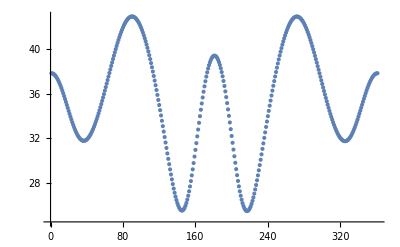

361

```mathematica
slice=meanRCS[[1]];
ListPlot[slice]
n=Length[slice]
```

```mathematica
dθ=π/180
```

π/180

```mathematica
a0=1/π∑_(k=1)^n
```

```mathematica
∑_(k=1)^n s■
```

```mathematica
a0=dθ/(2π)∑_(k=1)^360 slice[[k]]
```

35.2416

```mathematica
Mean[slice]
```

35.2488

## scratch

```mathematica
Range[3,30];
Length[%]
```

28

```mathematica
{Range[3,30],Range[1,28]}//TableForm
```

3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28

## movie

```mathematica
m=Length[meanRCS];
Do[
ν=k+2;
Print["frequency = ",ν," MHz"];
g000=ListPlot[meanRCS[[k]],PlotStyle->Black,Frame->True,Joined->True,
PlotRange->{-5,65},
PlotLabel->"Radar Frequency: "<>ToString[ν]<>" MHz",
ImagePadding->{{Automatic,4},{Automatic,Automatic}},
FrameLabel->{"Nose Angle","Mean Total RCS"},
FrameTicks->{{Automatic,Automatic},{{{0,-180},{90,-90},{180,0},{270,90},{361,180}},Automatic}}];
tresExport["cine-oth-"<>pad[ν],g000];
,{k,m}]
```

frequency = 3 MHz

frequency = 4 MHz

frequency = 5 MHz

frequency = 6 MHz

frequency = 7 MHz

frequency = 8 MHz

frequency = 9 MHz

frequency = 10 MHz

frequency = 11 MHz

frequency = 12 MHz

frequency = 13 MHz

frequency = 14 MHz

frequency = 15 MHz

frequency = 16 MHz

frequency = 17 MHz

frequency = 18 MHz

frequency = 19 MHz

frequency = 20 MHz

frequency = 21 MHz

frequency = 22 MHz

frequency = 23 MHz

frequency = 24 MHz

frequency = 25 MHz

frequency = 26 MHz

frequency = 27 MHz

frequency = 28 MHz

frequency = 29 MHz

frequency = 30 MHz

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```